# POSETS : A Mathematica Package PART 1: Basic Commands and Families of Posets

Curtis Greene, Eugenie Hunsicker, Department of Mathematics, Haverford College 19041, July 1990
Updates 1992-94:  John Dollhopf, Sam Hsiao, Curtis Greene
Updates 2008:  Erica Greene, Curtis Greene
Updates 2010-12:  Ian Burnette, Curtis Greene

## 1. Introduction

This document illustrates a Mathematica package designed to generate, display, and explore finite partially ordered sets ("posets"), emphasizing properties of use in combinatorics.   The package has two distinctive features: (1) a large repertoire of built-in examples (Boolean lattices, subword posets, lattices of partitions, distributive lattices, Young's lattice, Bruhat orders, etc.),  and (2) the ability to generate a poset directly from its formal definition, i.e., from a Mathematica program defining  its "covering function".  
A poset may also be defined by listing its covering pairs, or by giving any generating set of ordered pairs, or the incidence matrix corresponding to such a relation.  In addition, there are tools for constructing new posets from old: product and sum, subposet, distributive lattice of order ideals, etc.  
       
Once a poset has been generated (“built”), a large number of additional tools are available for studying its combinatorial structure.  These existing tools reflect the authors' combinatorial interests: enumerative invariants,  chains, multichains, antichains, rank generating functions, Mobius functions, linear extensions, and related topics.  A good reference for these topics is Richard Stanley's book, Enumerative Combinatorics V1 (Wadsworth, 1986). 

About this documentation: our intention has not been to write a "users manual", but rather to give an informal demonstration of  principal features.   The documentation consists of two segments:  Part 1 (this notebook) illustrates the basic commands by applying them to some well-known combinatorial families of posets.  Part 2 (a second notebook) contains more complicated examples and illustrations, as well as “case studies” illustrating applications to combinatorial problems of interest.

For a complete list of commands, one can print out the “usage” section of the package, which contains a precise description of the syntax for each command.
       
The package is available on the web at http://www.haverford.edu/math/cgreene.html. It is available in both notebook and plain ascii text formats. The authors welcome comments, questions, bug reports, criticisms, and other suggestions. Such communications should be directed to cgreene@haverford.edu, or to Curtis Greene, Department of Mathematics, Haverford College, Haverford PA 19041.

## 2. Basic Instructions

### Loading the package

The current version of the package (June 2012) is called Posets300.m. It may be placed in a directory or folder on Mathematica's search path for input. Windows users will typically put it in the AddOns/ExtraPackages folder. Directories on the current search path can be identified using the $Path command, for example, under Windows one gets.

```mathematica
$Path[] (*open cell to see an example*)
```

{C:\Program Files\Wolfram Research\Mathematica\8.0\SystemFiles\Links,C:\Users\CG\AppData\Roaming\Mathematica\Kernel,C:\Users\CG\AppData\Roaming\Mathematica\Autoload,C:\Users\CG\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\CG,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\LegacyPackages,C:\Program Files\Wolfram Research\Mathematica\8.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\8.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\8.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\8.0\Documentation\English\System}[]

Once the package has been placed in a proper directory, it can be loaded by typing

```mathematica
<<posets300.m
```

More simply, one can just open the file and click the "run package" button.

### Using the package

To generate a poset, type

```mathematica
Build[<def>,<name>]
```

where <def> is a "definition" (of one of three types, to be described below), and <name> is a string used to identify the poset in subsequent computations.  If no name is supplied, the  package creates one automatically.

The elements of a poset may be represented by any object recognized by Mathematica,  typically by lists, strings, or integers.  These objects become "labels" for elements of the poset.  A poset definition may have any one of the following forms:

(1)  A triple {f, <minlist>, H} , where f is a Mathematica function that generates, from an element w of P a list consisting of 
      its immediate successors (or covers); <minlist> is an explicit list of of the minimal elements of P; and H is an upper bound
      for the height of the poset (not necessarily the exact height.)

(2)  A pair {<relations>, N} , where N is an integer and <relations> is a set of pairs of integers ≤ N.  This should be an 
      acyclic relation generating the partial order.  It need not be a transitive relation, nor must it be a minimal generating set.

(3)  A matrix M, which is the incidence matrix of an acyclic relation generating the partial order.  Again, the relation represented by 
      M need not be transitive, nor must it be minimal.

The effect of

```mathematica
Build[<def>,<name>]
```

is to generate three fundamental objects associated with the poset:

(1)   An object P[<name>]. This is a list of the elements of P. The elements of P[<name>] serve as "labels" for P.  If P is 
       defined by order relations or by an incidence matrix, then the labels are just indices, i.e.  P[<name>] = 
       {1,2, ..., Card[P]}. 
       
(2)   An object Rank[<name>]. This is a list showing the rank of each element of P, defined (initially) as the length of the 
         longest chain descending from x. (If P is a "strongly ranked poset", these ranks coincide with the usual definition of rank. If
         not, they can be changed to produce different structural representations of P. See the note below.)  
         The indexing of the array Rank[<name>] agrees with  that of  P[<name>].  
              
(3)   An object CoverRelations[<name>]. This is a list of pairs of indices {i,j} that defines a minimal generating set for the 
       order relation.

All other commands and operations in the package refer to these objects, and many other derived objects are available.  For a full list of commands and objects, with precise syntax, refer to the "usage" portion of the package itself.  An index may be found at the end of this document.

In cases where obejcts or functions depend on results returned by other functions, these are called automatically. For example, many functions need to compute ZetaP[<name>], the incidence matrix of the transitive closure of the cover relation, and this is done automatically when required. The user need not be concerned with the order in which comands are executed.   Once computed, objects are "remembered", so that time is not wasted computing them again.

Elements of the poset are always maintained in a "natural", or topologically sorted order.  When P is a ranked (or graded) poset, the elements of each rank are grouped together, and a separate object PGraded[<name>][[k]] lists the elements of rank k.

This notebook was executed with build version

```mathematica
Ver
```

3.00dz4

#### Cautionary note about rank functions:

The values in Rank[name] initially give only a "first approximation", guaranteed to be valid only if P is a strongly ranked poset (the rank function is equal to the longest descending chain minus 1). If a P is not known to be ranked, it should be tested using the RankedQ[name] command, which determines whether it is ranked and also adjusts Rank[name] so that its values are correct (if possible). There is also a radio button in the Diagram/Manipulate dashboard that achieves the same result. The values in Rank[name] affect the posititions of elements computed by the Diagram command; thus a poset may look different before and after RankedQ is applied. See the section on MajP[n], the majorization order, for further discussion and examples.

## 3. Fundamental Families of Posets

### SUBSETS OF A SET

In the first example we generate the lattice of subsets of a 4-element set and compute several combinatorial invariants.  In this command, Sets[4] is the built-in "definition" of the poset, and sub4 is a "tag name" (chosen by the user) to reference all of the objects associated with this poset.

```mathematica
Build[Sets[4],sub4]
```

Building poset sub4  ...

Done

Once a poset has been "built", its Hasse diagram may be displayed:

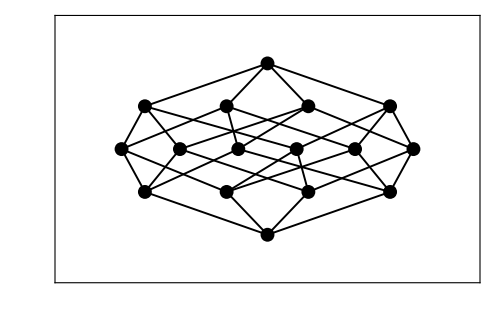

```mathematica
Diagram[sub4]
```

The elements of the poset may also be labeled, using the ShowLabels option. The yellow labels on the left show the “objects” of the poset; the blue labels on the right show the “indices” with which they may be referenced in the P[name] list.

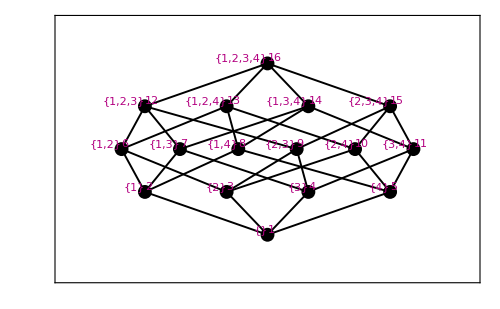

```mathematica
Diagram[sub4,ShowLabels->{1,2}]
```

Additional manipulation of the diagram is possible: stretching, changing the thickness of lines and points, adding a second set of labels, moving the labels around, identifying special sets of points. These features will be illustrated in later sections of this notebook.

All-purpose manipulation capability is provided by the Manipulate ⟶ True option.

```mathematica
Diagram[sub4,Manipulate->True]
```

12345

Building a poset generates four fundamental obejcts: P[sub4], Labels[sub4], Rank[sub4], and CoverRelations[sub4].

P[sub4] is a list of all the elements of the poset, in the form (and order) that they were generated.

```mathematica
P[sub4]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

Labels[sub4] is initially constructed as of two lists of labels. The lists the “elements” in the poset, and the second lists the “indices” used by the package to reference the elements.  Both labels may be attached to nodes in the diagram. Both lists may be redefined as desired, and re-displayed by the Diagram command, and additional lists of labels (3, 4, ...) may be added.

```mathematica
Labels[sub4][[1]]
Labels[sub4][[2]]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

Rank[sub4] is a list showing the “ranks” of each element. Initially, the rank of an element is defined as the length of the longest descending chain (minus 1). These ranks govern how the poset is displayed by the Diagram command.  When the poset is not a "ranked poset", these numbers need to be recomputed (see below) in order for Diagram to work correctly.

```mathematica
Rank[sub4]
```

{0,1,1,1,1,2,2,2,2,2,2,3,3,3,3,4}

CoverRelations[sub4] is a list of covering pairs of indices.

```mathematica
CoverRelations[sub4]
```

{{1,2},{1,3},{1,4},{1,5},{2,6},{2,7},{2,8},{3,6},{3,9},{3,10},{4,7},{4,9},{4,11},{5,8},{5,10},{5,11},{6,12},{6,13},{7,12},{7,14},{8,13},{8,14},{9,12},{9,15},{10,13},{10,15},{11,14},{11,15},{12,16},{13,16},{14,16},{15,16}}

Other functions as well as additional constructions and options use the above four objects for basic data.

#### Examples of functions that use the basic data

The coefficents of the rank generating function indicate how many elements are at each rank.  In the present example, these numbers are just binomial coeffients.

```mathematica
RGF[sub4]
PGraded[sub4]
```

1+4 q+6 q^2+4 q^3+q^4

{{{}},{{1},{2},{3},{4}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}},{{1,2,3},{1,2,4},{1,3,4},{2,3,4}},{{1,2,3,4}}}

We can inquire whether the poset is a lattice. The answer is, of course, "yes" in this case.

```mathematica
LatticeQ[sub4]
```

True

The Zeta Polynomial Z[n] of a poset P counts the number of multichains x1≤x2 ... ≤ xn-1 that can be formed from the elements of P.

```mathematica
ZetaPoly[sub4,n]
```

n^4

The command ZetaPoly[name,a,b,n] computes the Zeta polynomial of the interval [a,b] in P, where a and b are indices. When P is an interval [a,b] this is the same as  the number of multichains 
                                  a  = x0 ≤ x1 ≤ x2 ≤ ... ≤ xn   =  b 
between a and b.

```mathematica
Table[ZetaPoly[sub4,1,b,n],{b,1,Card[sub4]}]
```

{1,n,n,n,n,n^2,n^2,n^2,n^2,n^2,n^2,n^3,n^3,n^3,n^3,n^4}

#### Labeling options

New labels can be created using the NewLabel command. By default, these become Labels[name][[3]], Labels[name][[4]], etc. They can be displayed by giving the new number to Diagram as a ShowLabels option. (Syntax: NewLabel[name, list])

{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

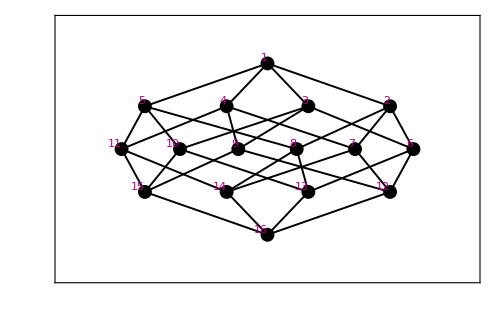

```mathematica
NewLabel[sub4,{16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}]
Labels[sub4][[3]]
Diagram[sub4,ShowLabels->3]
```

NewLabel can also take a function as a parameter. It will map the given function to the label in position 1 and create a new list of labels. (Syntax: NewLabel[name, function])

{0,1,1,1,1,2,2,2,2,2,2,3,3,3,3,4}

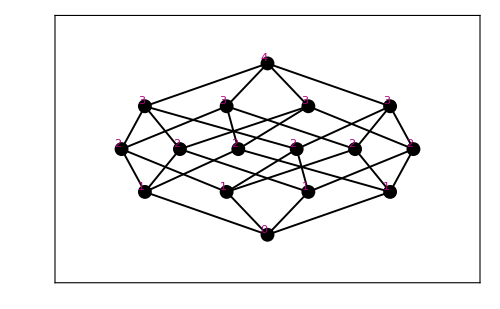

```mathematica
NewLabel[sub4,Length]
Labels[sub4][[4]]
Diagram[sub4,ShowLabels->4]
```

To manipulate existing labels we can use the ChangeLabel command. (Syntax: ChangeLabel[name, function, label number])

{False,False,False,True,False,True,False,False,False,True,False,True,False,True,True,False}

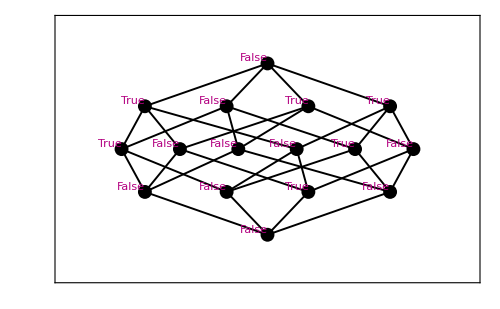

```mathematica
ChangeLabel[sub4,PrimeQ,3]
Labels[sub4][[3]]
Diagram[sub4,ShowLabels->3]
```

### PERMUTATIONS: WEAK ORDER

The (left) weak order on permutations is defined by saying that w covers u if w can be obtained from u by transposing a pair of adjacent increasing elements.

```mathematica
Build[WeakS[4],weaks4]
```

Building poset weaks4  ...

Done

```mathematica
P[weaks4]
```

{{1,2,3,4},{2,1,3,4},{1,3,2,4},{1,2,4,3},{2,3,1,4},{2,1,4,3},{3,1,2,4},{1,3,4,2},{1,4,2,3},{3,2,1,4},{2,3,4,1},{2,4,1,3},{3,1,4,2},{1,4,3,2},{4,1,2,3},{3,2,4,1},{2,4,3,1},{4,2,1,3},{3,4,1,2},{4,1,3,2},{3,4,2,1},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

The Hasse diagram for this poset may also be regarded as Cayley graph for the symmetric group S4, with respect to the generators (1,2), (2,3), (3,4).  For general Sn the Hasse diagram is a regular graph of degree n-1.

It is also possible to build the right weak order, defined by saying that w covers u if w can be obtained from u by transposing i and i+1 for some i.

```mathematica
Build[RWeakS[4],rweaks4]
```

Building poset rweaks4  ...

Done

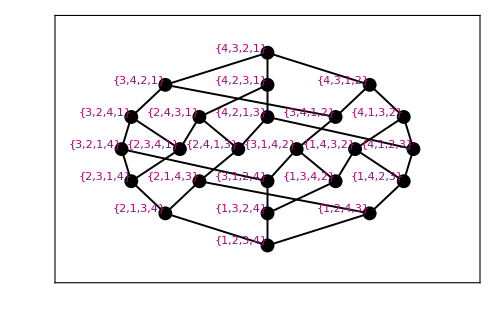

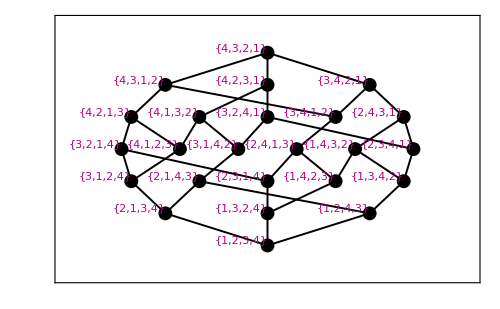

```mathematica
Diagram[weaks4,ShowLabels->1]
Diagram[rweaks4,ShowLabels->1]
```

Note that the diagrams are isomorphic, but the elements are different.

The rank generating function factors nicely (a well-known result).

```mathematica
RGF[weaks4]
Factor[RGF[weaks4]]
```

1+3 q+5 q^2+6 q^3+5 q^4+3 q^5+q^6

(1+q)^2 (1+q^2) (1+q+q^2)

The elements at each rank are stored and displayed in the order generated by the Build command. The poset can look quite different if another order is used.  For example, the command SortByRanks puts each rank into lexicographic order. Interestingly, in this case, the right and left weak orders behave differently.

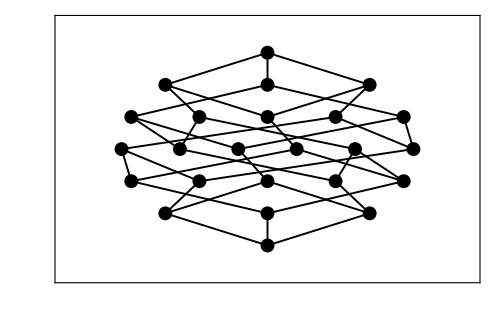

```mathematica
SortByRanks[weaks4]
Diagram[weaks4]
```

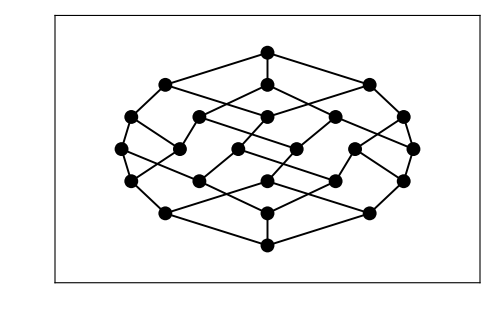

```mathematica
SortByRanks[rweaks4]
Diagram[rweaks4]
```

When combinatorial objects are represented by lists (as in this case), the labels are sometimes difficult to read. Compact command makes lists into strings, and ChangeLabel accepts the Compact function as input.

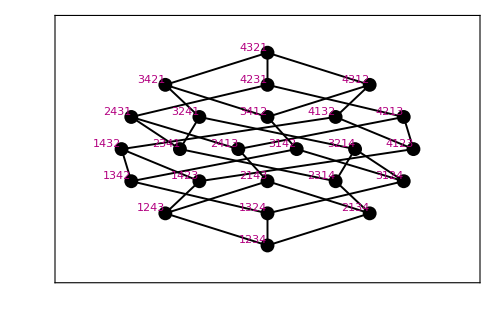

```mathematica
ChangeLabel[weaks4,Compact,1]
Diagram[weaks4,ShowLabels->1]
```

The ChangeLabel command may be given a list of labels instead of a function. For example, we can make the second set of labels equal to the poset elements, as follows. One can display the first and second labels simultaneously by using the ShowLabels->{1,2} option.

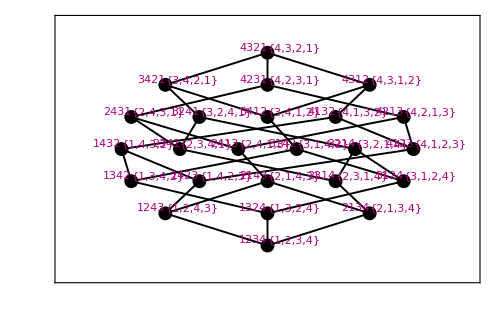

```mathematica
ChangeLabel[weaks4,P[weaks4],2]
Diagram[weaks4,ShowLabels->{1,2}]
```

In this example, the labels are somewhat difficult to read. To reposition labels and perform more complex adjustments, one can use the Manipulate option. For example, when the poset is large, it may be convenient to display the Hasse diagram with thinner dots and lines.  Clicking on the Save button in the Manipulate dashboard causes adjustments to be remembered and used in future executions of Display (try experimenting with this).

```mathematica
Build[WeakS[5],weaks5]
SortByRanks[weaks5]
Diagram[weaks5,Manipulate->True]
```

Building poset weaks5  ...

Done

12345

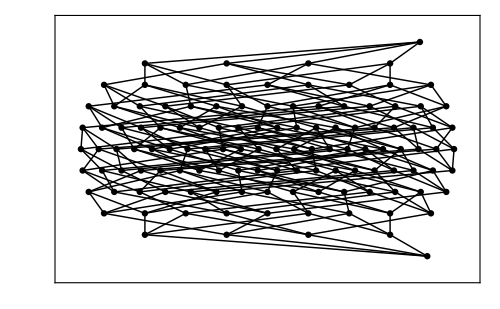

```mathematica
Diagram[weaks5]
```

The right weak order is obtained by applying the the weak order applied to the inverse permutation. We illustrate this by defining the second label (displayed in green below)  of a permutation in WeakS[4] to be its inverse, and then comparing with the diagram of RWeakS[4] above.

```mathematica
ChangeLabel[weaks4,P[weaks4],2]
ChangeLabel[weaks4,InversePermutation,2]
ChangeLabel[weaks4,Compact,2]
Diagram[weaks4,Manipulate->True]
```

12345

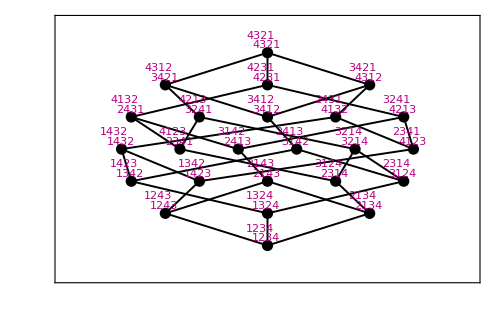

```mathematica
Diagram[weaks4,ShowLabels->{1,2}]
```

ShowLabels has several options:  
		{a,b}   :  displays labels #a and #b on left and right of the node
		{a} or a  : displays label #a to the left of the node
		{a,0}  : displays #a to the left of the node
		{0,b} : displays #b to the right of the node
		True : displays labels exactly as determined by the last Save executed in Manipulate
		False : displays no labels

### PERMUTATIONS: STRONG ORDER

The strong order on permutations (also known as the Bruhat order) is defined by saying that w is less than or equal to u if u can be obtained from w a sequence of length-increasing transpositions (not necessarily adjacent).

```mathematica
Build[StrongS[3],strong3]
```

Building poset strong3  ...

Done

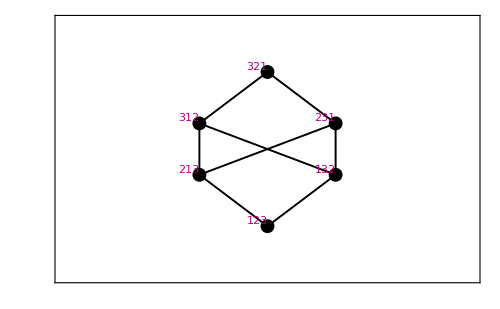

```mathematica
ChangeLabel[strong3,Compact,1]
Diagram[strong3,ShowLabels->1]
```

Building poset strongs4  ...

Done

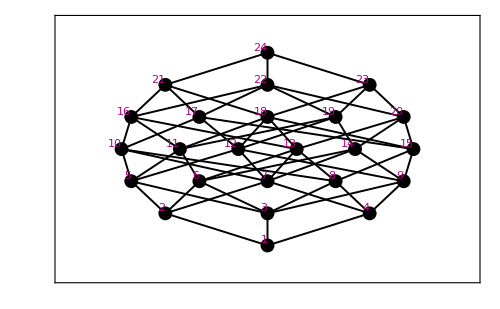

```mathematica
Build[StrongS[4],strongs4]
Diagram[strongs4,ShowLabels->2]
```

The strong order on Sn is not a lattice:

```mathematica
LatticeQ[strong3]
```

Not a lattice: P[3] and P[2] have no LUB.

False

### PARTITIONS OF A SET: REFINEMENT ORDER

In the refinement order on partitions of a set, partition A is less than or equal to partition B if every block of A is contained in a block of B.

```mathematica
Build[SetP[5],setp5]
```

Building poset setp5  ...

Done

The total number of partitions of a set of n elements is the nth Bell Number, usually denoted Bn.

```mathematica
Card[setp5]
```

52

The numbers of elements at each rank are given by Stirling numbers of the second kind. These may also be produced by the built-in Mathematica function StirlingS2.

```mathematica
RGF[setp5]
```

1+10 q+25 q^2+15 q^3+q^4

```mathematica
Table[StirlingS2[5,k],{k,5,1,-1}]
```

{1,10,25,15,1}

The characteristic polynomial of a poset with a 0 and 1 is a generalization of the chromatic polynomial of a graph. It is given by the formula   
                           CharPoly(q) =  ∑  μ(0,x) qr(1) -r(x)
where r denotes the rank function, μ denotes the Mobius function, and the sum is over all elements x in the poset.  For the lattice of partitions of {1,...,n} the characteristic polynomial is  the chromatic polynomial of Kn, the complete graph on n vertices (apart from a factor of q). This polynomial is of course just
                                           q (q-1) (q-2)  ...  (q-n+1)
Hence its coefficients are Stirling numbers of the first kind.  This may be checked using the built-in function StirlingS1.

```mathematica
CharPoly[setp5,q]
Factor[%]
```

24-50 q+35 q^2-10 q^3+q^4

(-4+q) (-3+q) (-2+q) (-1+q)

```mathematica
Table[StirlingS1[5,k],{k,1,5}]
```

{24,-50,35,-10,1}

Building poset setp4  ...

Done

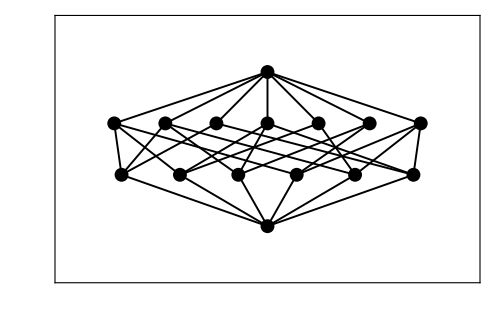

```mathematica
Build[SetP[4],setp4]
Diagram[setp4]
```

Partitions are represented in P[setp5] using "pointer" notation, i.e. by a list in which the kth entry is equal to the smallest integer in the block containing k.

```mathematica
P[setp4]
```

{{1,2,3,4},{1,1,3,4},{1,2,1,4},{1,2,3,1},{1,2,2,4},{1,2,3,2},{1,2,3,3},{1,1,1,4},{1,1,3,1},{1,1,3,3},{1,2,1,1},{1,2,1,2},{1,2,2,1},{1,2,2,2},{1,1,1,1}}

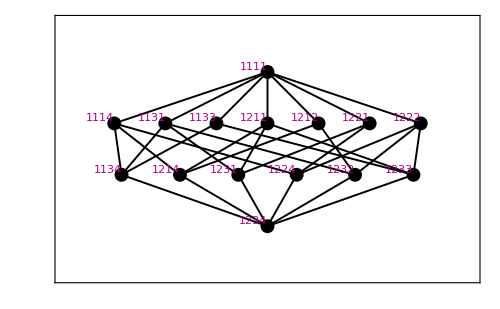

```mathematica
ChangeLabel[setp4,Compact,1]
Diagram[setp4,ShowLabels->1]
```

### NON-CROSSING PARTITIONS.

A partition is non-crossing if, when represented as above using pointer notation, it has no subsequence

```mathematica
{...,x,...,y,...,x,...,y,...}
```

with x not equal to y.  The non-crossing partitions form a very interesting sub-poset of SetP[n].

```mathematica
Build[NonXP[5],nxp5]
```

Building poset nxp5  ...

Done

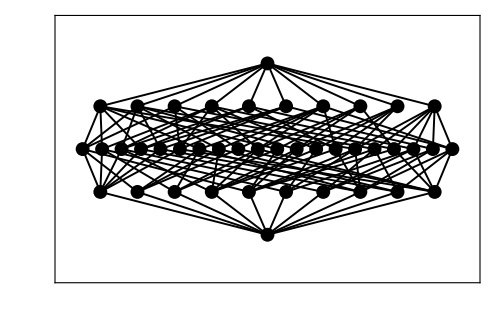

```mathematica
Diagram[nxp5]
```

```mathematica
LatticeQ[nxp5]
```

True

```mathematica
RGF[nxp5]
```

1+10 q+20 q^2+10 q^3+q^4

So it is a lattice, and is also rank-symmetric. It is interesting to note that both the cardinality and the Möbius function (from bottom to top) are Catalan numbers:

```mathematica
Card[nxp5]
```

42

```mathematica
Mu[nxp5]⟦1⟧
```

{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,2,2,2,1,1,1,2,2,1,2,1,1,1,1,2,2,1,2,1,2,-5,-5,-2,-5,-2,-2,-5,-2,-2,-5,14}

The number of maximal chains (from bottom to top) equals nn-2, which is also the number of spanning trees in the complete graph on n vertices. (This remarkable result, as well as others mentioned in this section, are due to G. Kreweras, Discrete Math. 1 (1972), 333-350.)

```mathematica
MaximalChainsDown[nxp5]
```

{1,1,1,1,1,1,1,1,1,1,1,3,3,3,2,2,2,3,3,2,3,2,2,2,2,3,3,2,3,2,3,16,16,9,16,9,9,16,9,9,16,125}

The elements of P[nxp5] are partitions and can be expressed in the same was as ordinary partitions, using pointer notation:

```mathematica
P[nxp5]
```

{{1,2,3,4,5},{1,1,3,4,5},{1,2,1,4,5},{1,2,3,1,5},{1,2,3,4,1},{1,2,2,4,5},{1,2,3,2,5},{1,2,3,4,2},{1,2,3,3,5},{1,2,3,4,3},{1,2,3,4,4},{1,1,1,4,5},{1,1,3,1,5},{1,1,3,4,1},{1,1,3,3,5},{1,1,3,4,3},{1,1,3,4,4},{1,2,1,1,5},{1,2,1,4,1},{1,2,1,4,4},{1,2,3,1,1},{1,2,2,1,5},{1,2,2,4,1},{1,2,3,2,1},{1,2,3,3,1},{1,2,2,2,5},{1,2,2,4,2},{1,2,2,4,4},{1,2,3,2,2},{1,2,3,3,2},{1,2,3,3,3},{1,1,1,1,5},{1,1,1,4,1},{1,1,1,4,4},{1,1,3,1,1},{1,1,3,3,1},{1,1,3,3,3},{1,2,1,1,1},{1,2,2,1,1},{1,2,2,2,1},{1,2,2,2,2},{1,1,1,1,1}}

Next we investigate how NonXP[n] "sits" inside SetP[n].  The first step is use LocateSet to determine the indices corresponding to a particular set of elements in a poset.  In this case, we locate the indices corresponding to P[nxp5] in P[setp5].

```mathematica
nxpindices=LocateSet[setp5,P[nxp5]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,22,23,24,27,28,29,30,31,32,33,35,36,37,38,39,40,42,43,44,48,50,51,52}

The same result can be obtained using the SpecialPoints[name,function] command, which picks out of P[name] the indices for which function returns the value True.

```mathematica
NonCrossing[{___,x_,___,y_,___,x_,___,y_,___}] := False /; x!=y
NonCrossing[{___}] := True
SpecialPoints[setp5,NonCrossing]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,22,23,24,27,28,29,30,31,32,33,35,36,37,38,39,40,42,43,44,48,50,51,52}

Now we can check some other things:

```mathematica
SubLatticeQ[setp5,nxpindices]
JoinSubLatticeQ[setp5,nxpindices]
MeetSubLatticeQ[setp5,nxpindices]
```

False

False

True

So the non-crossing partitions are closed under forming meets but not joins. For example:

```mathematica
JoinL[nxp5,{1,2,3,3,2},{1,2,1,4,5}]
```

{1,1,1,1,1}

```mathematica
JoinL[setp5,{1,2,3,3,2},{1,2,1,4,5}]
```

{1,2,1,1,2}

```mathematica
MeetL[nxp5,{1,2,3,3,2},{1,2,1,4,5}]
```

{1,2,3,4,5}

```mathematica
MeetL[setp5,{1,2,3,3,2},{1,2,1,4,5}]
```

{1,2,3,4,5}

One can ask Display to highlight any subset of points. For example, here is a diagram of SetP[5], highlighting the elements of NonXP[5]:

```mathematica
ChangeLabel[setp5,Compact,1]
```

```mathematica
Diagram[setp5,nxpindices, Manipulate->True]
```

12345

### LATTICE OF CONTRACTIONS OF A GRAPH.

If G is a graph with vertex set V, the set of partitions of V whose blocks are G-connected forms a join-sublattice of the full partition lattice on V, called the lattice of contractions of G.  We illustrate by constructing this lattice when G is a 5-cycle.

Building poset cycle5  ...

Done

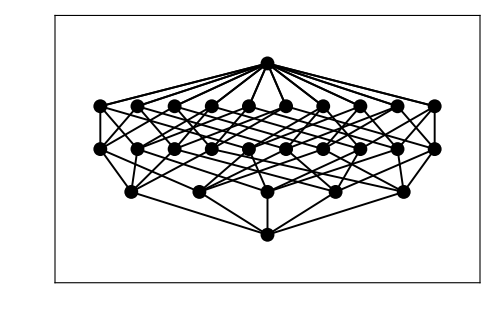

```mathematica
edgeset={{1,2},{2,3},{3,4},{4,5},{5,1}};
Build[ContractionLattice[edgeset,5],cycle5]
Diagram[cycle5]
```

The elements of P[cycle5] are partitions of {1,2,3,4,5}, represented (as before) using pointer notation.

```mathematica
P[cycle5]
```

{{1,2,3,4,5},{1,1,3,4,5},{1,2,2,4,5},{1,2,3,3,5},{1,2,3,4,4},{1,2,3,4,1},{1,1,1,4,5},{1,1,3,3,5},{1,1,3,4,4},{1,1,3,4,1},{1,2,2,2,5},{1,2,2,4,4},{1,2,2,4,1},{1,2,3,3,3},{1,2,3,3,1},{1,2,3,1,1},{1,1,1,1,5},{1,1,1,4,4},{1,1,1,4,1},{1,1,3,3,3},{1,1,3,3,1},{1,1,3,1,1},{1,2,2,2,2},{1,2,2,2,1},{1,2,2,1,1},{1,2,1,1,1},{1,1,1,1,1}}

Let's see what this set looks like, as a subset of P[set5].

```mathematica
c5indices=LocateSet[setp5,P[cycle5]]
```

{1,2,5,6,9,11,12,14,15,17,23,27,29,30,32,36,37,38,39,40,42,43,44,48,50,51,52}

```mathematica
SubLatticeQ[setp5,c5indices]
JoinSubLatticeQ[setp5,c5indices]
MeetSubLatticeQ[setp5,c5indices]
```

False

True

False

So, as remarked earlier, it is a join-sublattice of P[set5], but is not closed under meets.

```mathematica
Diagram[setp5,c5indices,Manipulate->True]
```

12345

The characteristic polynomial of the lattice of contractions of a graph G is equal to the chromatic polynomial of G (apart from a factor of q) .

```mathematica
CharPoly[cycle5,q]
```

4-10 q+10 q^2-5 q^3+q^4

It is well-known that the chromatic polynomial of an n-cycle can be expressed by the formula
                                   (q - 1)n + (-1)n (q - 1)
We can check the above result by computing,  for n=5,

```mathematica
Expand[(q-1)^n+(-1)^n (q-1)/.n->5]
```

4 q-10 q^2+10 q^3-5 q^4+q^5

The coefficients of the characteristic polynomial (and in this case the chromatic polynomial) are obtained by summing the Mobius function μ(0,x) over each rank.  This can be illustrated and checked by labelling each element by its Mobius function value, as follows:

```mathematica
Labels[cycle5][[1]]
```

{{1,2,3,4,5},{1,1,3,4,5},{1,2,2,4,5},{1,2,3,3,5},{1,2,3,4,4},{1,2,3,4,1},{1,1,1,4,5},{1,1,3,3,5},{1,1,3,4,4},{1,1,3,4,1},{1,2,2,2,5},{1,2,2,4,4},{1,2,2,4,1},{1,2,3,3,3},{1,2,3,3,1},{1,2,3,1,1},{1,1,1,1,5},{1,1,1,4,4},{1,1,1,4,1},{1,1,3,3,3},{1,1,3,3,1},{1,1,3,1,1},{1,2,2,2,2},{1,2,2,2,1},{1,2,2,1,1},{1,2,1,1,1},{1,1,1,1,1}}

```mathematica
Mu[cycle5][[1]]
```

{1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,4}

```mathematica
ChangeLabel[cycle5,Mu[cycle5]⟦1⟧,1]
```

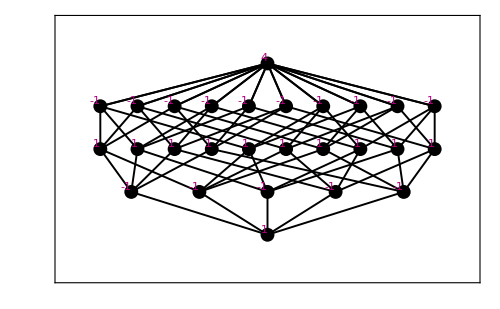

```mathematica
Diagram[cycle5,ShowLabels->1]
```

Observe that the sums of the labels across each row give the coefficients of the chararacteristic polynomial.

### YOUNG'S LATTICE

Let L be a partition. Then YoungsLattice[L] is the poset consisting of partitions whose Ferrers diagram fits inside the Ferrers diagram of L. The partial ordering is by containment of diagrams.  This turns out to be a distributive lattice, and from its poset of join-irreducibles one recovers the original Ferrers diagram of L.  Maximal chains in YoungsLattice[L] are in one-to-one correspondence with standard Young tableaux of shape L.

```mathematica
Build[YoungsLattice[{5,2,2,1,1}],y52211]
```

Building poset y52211  ...

Done

The list P[y52211] contains all partitions whose Ferrers diagram fits inside the Ferrers diagram of L = {5,2,2,1,1}. They are padded with trailing zeros, out to the length of the original partition.

```mathematica
P[y52211]
```

{{0,0,0,0,0},{1,0,0,0,0},{2,0,0,0,0},{1,1,0,0,0},{3,0,0,0,0},{2,1,0,0,0},{1,1,1,0,0},{4,0,0,0,0},{3,1,0,0,0},{2,2,0,0,0},{2,1,1,0,0},{1,1,1,1,0},{5,0,0,0,0},{4,1,0,0,0},{3,2,0,0,0},{3,1,1,0,0},{2,2,1,0,0},{2,1,1,1,0},{1,1,1,1,1},{5,1,0,0,0},{4,2,0,0,0},{4,1,1,0,0},{3,2,1,0,0},{3,1,1,1,0},{2,2,2,0,0},{2,2,1,1,0},{2,1,1,1,1},{5,2,0,0,0},{5,1,1,0,0},{4,2,1,0,0},{4,1,1,1,0},{3,2,2,0,0},{3,2,1,1,0},{3,1,1,1,1},{2,2,2,1,0},{2,2,1,1,1},{5,2,1,0,0},{5,1,1,1,0},{4,2,2,0,0},{4,2,1,1,0},{4,1,1,1,1},{3,2,2,1,0},{3,2,1,1,1},{2,2,2,1,1},{5,2,2,0,0},{5,2,1,1,0},{5,1,1,1,1},{4,2,2,1,0},{4,2,1,1,1},{3,2,2,1,1},{5,2,2,1,0},{5,2,1,1,1},{4,2,2,1,1},{5,2,2,1,1}}

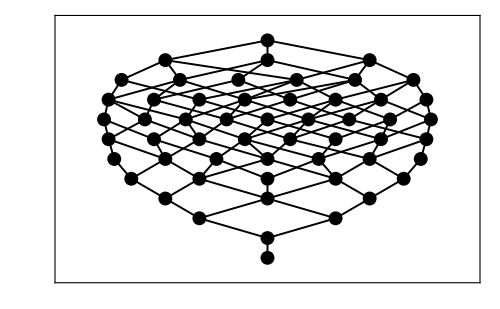

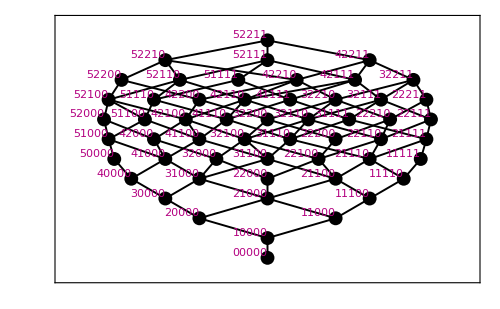

```mathematica
ChangeLabel[y52211,Compact,1];
Diagram[y52211]
Diagram[y52211,ShowLabels->1]
```

We get the number of standard Young tableaux associated with each element of P[y52211] by computing maximal chains, as follows:

```mathematica
MaximalChainsDown[y52211]
```

{1,1,1,1,1,2,1,1,3,2,3,1,1,4,5,6,5,4,1,5,9,10,16,10,5,9,5,14,15,35,20,21,35,15,14,14,64,35,56,90,35,70,64,28,120,189,70,216,189,162,525,448,567,1540}

We can illustrate the diagram with labels showing, for each partitions, the number of standard tableaux of that shape.

The last number in this list (i.e., the number of chains from bottom to top) can also be obtained by applying the famous "hook formula" :

```mathematica
11!/(9 6 3 2 1 5 2 4 1 2 1)
```

1540

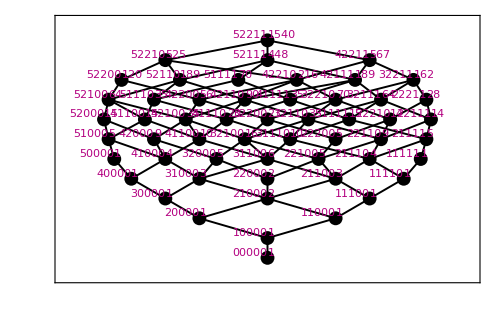

```mathematica
ChangeLabel[y52211,MaximalChainsDown[y52211],2]
Diagram[y52211,ShowLabels->{1,2}]
```

P[y52211] is a distributive lattice, and thus its join- and meet-irreducibles are of particular interest. In fact we would like to identify the entire "poset of join-irreducibles", for separate study. The following command locates the indices of the join-irreducibles.

```mathematica
JI[y52211]
```

{2,3,4,5,7,8,10,12,13,19,25}

Next we  produce another diagram of P[y52211], with the join-irreducibles highlighted. Since it is usually difficult (in large cases) to verify the order relation visually, we can also highlight cover relations in the poset of join-irreducibles.  (Any subposet and/or collection of links may be highlighted this way).

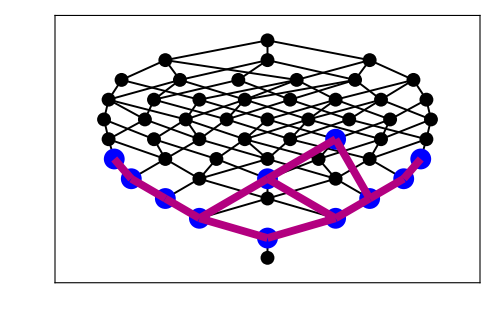

```mathematica
Diagram[y52211,JI[y52211],JICoverRelations[y52211]]
```

In the shaded segments of the subposet one can see the Ferrers diagram for {5,2,2,1,1}.  The poset itself can be extracted using the SubPoset command. To use this command, one needs the name of the original poset, as well as a set of indices to pick out. (The indices may be generated in other ways; see Section 4 for more examples and further discussion of the SubPoset command.)

{2,3,4,5,7,8,10,12,13,19,25}

Building Subposet jisub  ...

Building poset jisub  ...

Done

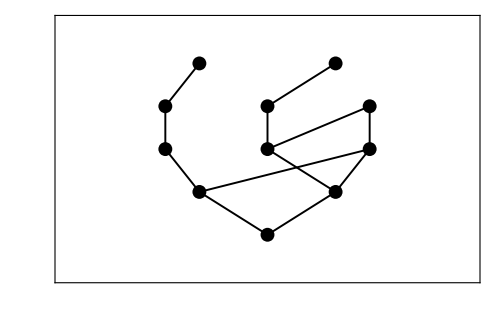

```mathematica
indices=JI[y52211]
BuildSubPoset[y52211,indices,jisub]
Diagram[jisub]
```

Unfortunately the Diagram and SubPoset commands cannot extract something that "looks" more like a Ferrers diagram than the two versions you see above. However, there is a separate Ferrers command that does a slightly better job:

Building poset f5221  ...

Done

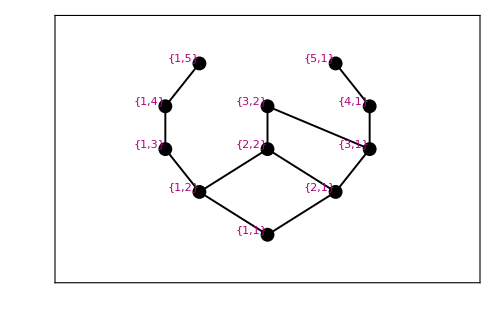

```mathematica
Build[Ferrers[{5,2,2,1,1}],f5221]
Diagram[f5221,ShowLabels->1]
```

### DIVISORS OF AN INTEGER

The divisors of N form a poset (actually a distributive lattice) under the divisibility relation. Each element (an integer) may be identified with the multiset of primes occurring in its prime factorization. Hence this lattice may  also be viewed as the lattice of multisubsets of a multiset.

Building poset d210  ...

Done

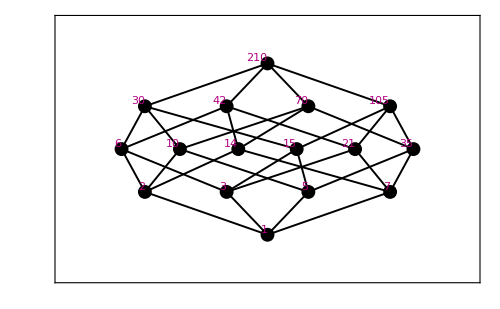

```mathematica
Build[Div[210],d210]
Diagram[d210,ShowLabels->1]
```

When N is squarefree (as in this case), it Div[N] is isomorphic to a subset lattice.

```mathematica
FactorInteger[210]
```

{{2,1},{3,1},{5,1},{7,1}}

Here is a non - squarefree example :

Building poset d288  ...

Done

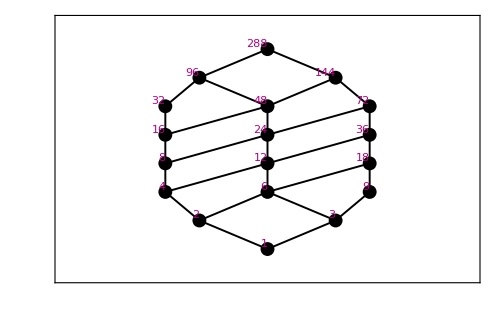

```mathematica
Build[Div[288],d288]
Diagram[d288,ShowLabels->1]
```

```mathematica
FactorInteger[288]
```

{{2,5},{3,2}}

It is well-known that this poset is a distributive lattice. In general, the command DistributiveLatticeQ can be used to test this property.

```mathematica
DistributiveLatticeQ[d288]
```

True

The Mobius function of this poset is the "classical" number-theoretic Mobius function.  In this context, its values may defined as the entries of the inverse of the Zeta-matrix of P.

```mathematica
Mu[d288]//MatrixForm
```

(1 | -1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Exercise for the reader: what formula generates the numbers illustrated by the next command?

```mathematica
MaximalChainsDown[d288]
```

{1,1,1,1,2,1,1,3,3,1,4,6,1,5,10,6,15,21}

### PARTITIONS OF AN INTEGER N : REFINEMENT ORDER

Partitions of fixed integer N form a poset under the "refinement" ordering (the definition should be clear). It is a curious poset, because most of the known results concerning it are negative.  For example, it is not a lattice, it's Mobius function does not alternate in sign, etc.  Is there anything nice to say about this poset?

```mathematica
Build[NumP[8],nump8]
```

Building poset nump8  ...

Done

```mathematica
P[nump8]
```

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,2},{1,1,1,1,1,3},{1,1,1,1,2,2},{1,1,1,1,4},{1,1,1,2,3},{1,1,2,2,2},{1,1,1,5},{1,1,2,4},{1,1,3,3},{1,2,2,3},{2,2,2,2},{1,1,6},{1,2,5},{1,3,4},{2,2,4},{2,3,3},{1,7},{2,6},{3,5},{4,4},{8}}

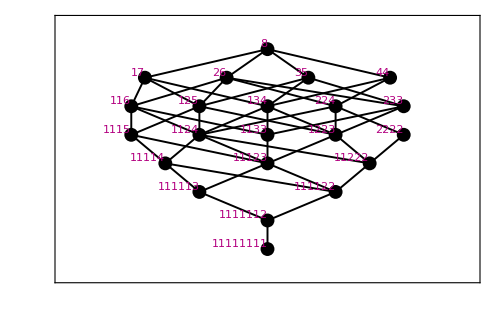

```mathematica
ChangeLabel[nump8,Compact,1]
Diagram[nump8,ShowLabels->1]
```

This poset is definitely not a lattice, as the following shows:

```mathematica
LatticeQ[nump8]
```

Not a lattice: P[4] and P[3] have no LUB.

False

Question: does anybody know a formula for the following numbers?

```mathematica
MaximalChainsDown[nump8]
```

{1,1,1,1,2,2,1,4,5,2,3,1,11,12,10,9,5,33,37,27,19,116}

```mathematica
MaximalChainsUp[nump8]
```

{116,116,47,69,15,32,22,5,10,7,10,2,2,3,3,2,2,1,1,1,1,1}

### PARTITIONS OF AN INTEGER N: DOMINANCE ORDER

The partitions of a fixed integer N have another natural ordering, defined as follows.  We say that A is less than or equal to B if, for all k, the sum of the k largest parts of A is less than or equal to the sum of the k largest parts of B. This is known as the dominance, or majorization order, and gives a poset with extremely interesting properties. The dominance order appears naturally in problems related to symmetric functions, characters of Sn, zero-one matrices, and many other subjects. For an extensive survey, see the book by A. W. Marshall and I. Olkin, "Inequalities: Theory of Majorization and its Applications", Academic Press (1979).

```mathematica
Build[MajP[9],majp9]
```

Building poset majp9  ...

Done

```mathematica
P[majp9]
```

{{1,1,1,1,1,1,1,1,1},{2,1,1,1,1,1,1,1},{2,2,1,1,1,1,1},{2,2,2,1,1,1},{3,1,1,1,1,1,1},{2,2,2,2,1},{3,2,1,1,1,1},{3,2,2,1,1},{4,1,1,1,1,1},{3,2,2,2},{3,3,1,1,1},{4,2,1,1,1},{3,3,2,1},{4,2,2,1},{5,1,1,1,1},{3,3,3},{4,3,1,1},{5,2,1,1},{4,3,2},{5,2,2},{6,1,1,1},{4,4,1},{5,3,1},{6,2,1},{5,4},{6,3},{7,1,1},{7,2},{8,1},{9}}

The majorization poset is an interesting example of a poset that is not “ranked”.  By definition, a poset is ranked if for every x < y, all maximal chains between x and y have the same length. A close examination of the following diagram shows that P[majp9] fails to have this property.

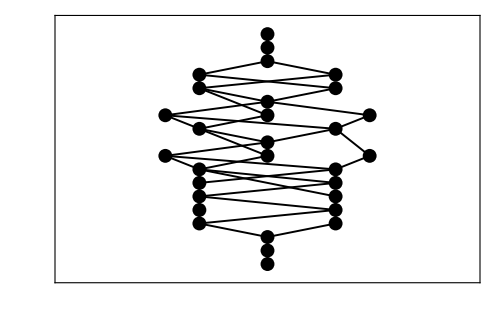

```mathematica
Diagram[majp9]
```

If a poset is known to be not ranked (or not known to be ranked), it is usually a good idea to execute RankedQ[name] immediately after the Build[name] command. This confirms (by returning True or False) whether the poset is ranked, and also adjusts Rank[name] so that the its values are correct when a rank function exists, and otherwise redefines Rank[name] so that rank(x)= height(x), i.e. the length of the longest chain descending from x (minus 1). The Build command returns these results automatically in most but not all cases. Executing RankedQ[name] is always safe, but can be time-consuming for large posets. [See the next section for a more technical discussion.]

```mathematica
RankedQ[majp9]
```

False

The following diagram shows each element of P[maj9] labeled by its height.

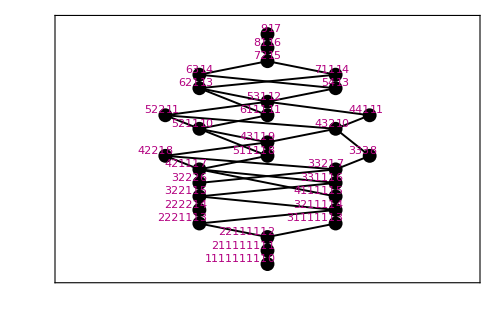

```mathematica
ChangeLabel[majp9,Compact,1]
ChangeLabel[majp9,Rank[majp9],2]
Diagram[majp9,ShowLabels->{1,2}]
```

Even though P[majp9] is not ranked, it does have the nice property of being a lattice.

```mathematica
LatticeQ[majp9]
```

True

It is also self-dual. We can verify this using the command IsomorphicQ, which tests for isomorphism and also generates a map if the result is True.

```mathematica
BuildDual[majp9,dualp9]
IsomorphicQ[majp9,dualp9]
```

Building poset dualp9  ...

Done

True

If the result of applying IsomorphicQ is True, an isomorphism map may be recovered using the GetIsomorphism command.

```mathematica
iso=GetIsomorphism[majp9,dualp9]
```

{1,2,3,5,4,6,7,8,9,10,11,13,12,14,16,15,17,19,18,20,22,21,23,24,25,27,26,28,29,30}

As expected, this isomorphism associates every partition with its conjugate :

```mathematica
{P[majp9],P[dualp9][[iso]]}//Transpose//Column
```

{{1,1,1,1,1,1,1,1,1},{9}}
{{2,1,1,1,1,1,1,1},{8,1}}
{{2,2,1,1,1,1,1},{7,2}}
{{2,2,2,1,1,1},{6,3}}
{{3,1,1,1,1,1,1},{7,1,1}}
{{2,2,2,2,1},{5,4}}
{{3,2,1,1,1,1},{6,2,1}}
{{3,2,2,1,1},{5,3,1}}
{{4,1,1,1,1,1},{6,1,1,1}}
{{3,2,2,2},{4,4,1}}
{{3,3,1,1,1},{5,2,2}}
{{4,2,1,1,1},{5,2,1,1}}
{{3,3,2,1},{4,3,2}}
{{4,2,2,1},{4,3,1,1}}
{{5,1,1,1,1},{5,1,1,1,1}}
{{3,3,3},{3,3,3}}
{{4,3,1,1},{4,2,2,1}}
{{5,2,1,1},{4,2,1,1,1}}
{{4,3,2},{3,3,2,1}}
{{5,2,2},{3,3,1,1,1}}
{{6,1,1,1},{4,1,1,1,1,1}}
{{4,4,1},{3,2,2,2}}
{{5,3,1},{3,2,2,1,1}}
{{6,2,1},{3,2,1,1,1,1}}
{{5,4},{2,2,2,2,1}}
{{6,3},{2,2,2,1,1,1}}
{{7,1,1},{3,1,1,1,1,1,1}}
{{7,2},{2,2,1,1,1,1,1}}
{{8,1},{2,1,1,1,1,1,1,1}}
{{9},{1,1,1,1,1,1,1,1,1}}

Here is one more illustration of diagramming posets with "special points" displayed.  The command SpecialPoints[name,function] returns the indices in P[name] for which function evaluates as True, and the result can be given directly as an option to Diagram.  For example:

```mathematica
SpecialPoints[majp9, Length[#]≥  5&]
```

{1,2,3,4,5,6,7,8,9,11,12,15}

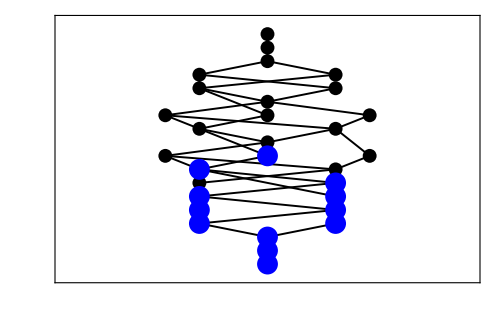

```mathematica
Diagram[majp9,SpecialPoints[majp9, Length[#]≥  5&]]
```

Try executing the following command and playing with the slider.

```mathematica
Manipulate[Diagram[majp9,SpecialPoints[majp9, Length[#]≥  k&]],{k,10,1,-1}]
```

### RANKED AND STRONGLY RANKED POSETS (TECHNICAL)

By definition, a poset P is ranked if there exists an integer-valued function r defined on P such that r(x) = r(y+1) whenever x covers y in P. If P is a ranked poset and has a unique minimal element (often the case in combinatorial situations), then executing Build always constructs a valid rank function: these are the entries in Rank[name].

If P is not a ranked poset, then Rank[name] may contain a different result. If P is generated using the Build[{relations, n}, name] or Build[matrix, name] commands, Rank[name] is automatically defined in terms of height, i.e., rank(x) equals the length of the longest chain descending from x (minus 1). For most non-ranked posets, this is a natural alternate definition of rank. Moreover, it produces a reasonable diagram because comparable elements will never have the same rank.

If a poset is generated using the Build[{f, minlist,h},name] command (i.e., the poset is generated from its covering function) the rank of an element is defined recursively, i.e., rank(x) = rank(y)+1 if y is the element that first generates x.  For non-ranked posets, this may not agree with the definition based on height. If Diagram were to use this rank function to arrange elements, it could produce undesirable results since covering pairs might be at the same level.

Even when P is ranked, using the height function as rank may not produce the “best” diagram, since a poset with several minimal elements can have a rank function but not satisfy rank(x) = height(x) for all x.

To produce a more appropriate rank function in all of these situations (and hence a better diagram), one can execute the query RankedQ[name], which performs the following steps.  First it checks (by solving linear equations) to see if a rank function exists. If so, then Rank[name] is redefined to use that function. Otherwise, Rank[name] is redefined using height. In both cases, other objects that depend on Rank[name] (for example, PGraded, NK, RGF, and H) are redefined as necessary. Finally, RankedQ returns True or False depending on the result.

In fact the Diagram command automatically executes RankedQ, so the above step is not necessary if one executes Diagram immediately after Build, i.e.,

```mathematica
Build[def,name]
Diagram[name]
```

In rare cases, since executing RankedQ can be time - consuming for large posets, one can execute diagram with the option CleanRank -> False to suppress execution of RankedQ.  One might do this if one is not interested in the rank structure or in a diagram.

We illustrate with a simple example of a poset that is ranked, but for which the intitial values of Rank[name] are not a rank function. The red labels show the original “elements” of the poset and the blue labels show the original “rank”, which in this case equals “height”.  Then RankedQ[name] is executed, which produces different ranks (now correct) and a nicer picture.

Building poset oddposet1  ...

Done

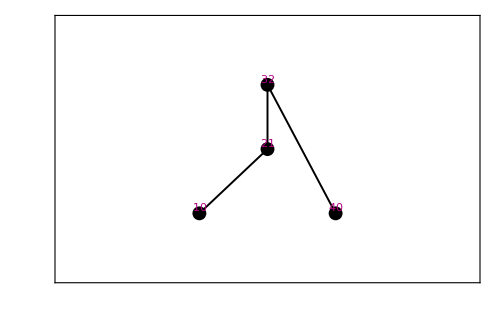

```mathematica
Build[{{{1,2},{2,3},{4,3}},4},oddposet1]
ChangeLabel[oddposet1,Rank[oddposet1],2]
Diagram[oddposet1,ShowLabels->{1,2},CleanRank->False]
```

True

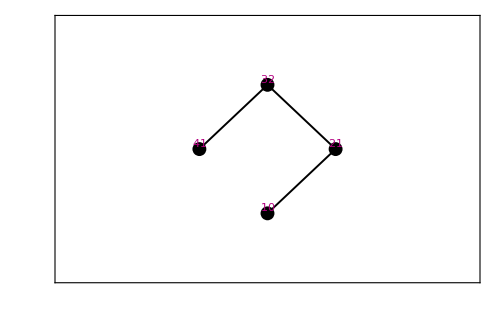

```mathematica
RankedQ[oddposet1]
ChangeLabel[oddposet1,Rank[oddposet1],2]
Diagram[oddposet1,ShowLabels->{1,2}]
```

We call a ranked poset strongly ranked if all of its minimal elements have rank zero.

```mathematica
RankedQ[oddposet1]
StrongRankedQ[oddposet1]
```

True

False

### RANDOM POSETS

Random posets may be produced with the command Build[Random[N,p]], which generates ordered pairs{a,b} satisfying  a<b, each with probability p, and then forms the transitive closure.

Building poset ran21  ...

Done

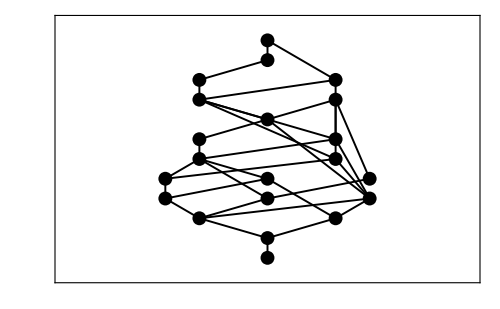

```mathematica
Build[RandomP[21,.5],ran21]
Diagram[ran21]
```

Since these random posets are rarely ranked, the Hasse diagram often looks "wrong" unless the standard uniform alignment of vertices is perturbed slightly. This can be done manually manipulating ranks using the “Points and Lines” tab in the Manipulate control panel (try it!).  For unranked posets, this should be done whenever consecutive segments passing through a vertex in the Hasse diagram appear to be parallel.

```mathematica
Diagram[ran21,Manipulate->True]
```

12345

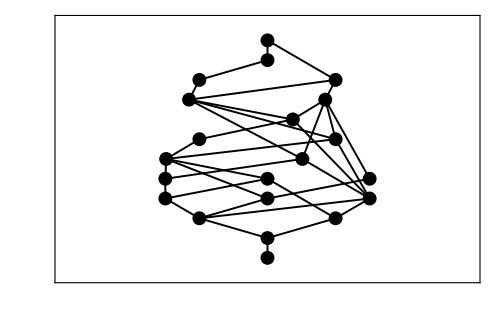

```mathematica
Diagram[ran21]
```

As noted before, when a poset is not ranked and either RankedQ or Diagram are called, the Rank object is redefined so that the rank of an element equals its "height", i.e., length of the longest chain descending from it, minus one. Exercise: verify this for the above poset. Second exercise: re-display the poset with labels showing the height of each element.

```mathematica
Rank[ran21]
```

{0,1,2,2,3,3,3,4,4,4,5,5,6,6,7,8,8,9,9,10,11}

```mathematica
P[ran21]
```

{1,2,3,6,4,5,7,8,9,16,10,12,11,14,13,15,18,17,19,20,21}

## 4. Operations on Posets

### ELEMENTARY CONSTRUCTIONS

In this section we illustrate some simple commands for building new posets from old ones: DisjointSum, OrdinalSum, and CProduct (short for CartesianProduct, which was changed to avoid a conflict with the Combinatorica package).  Two other commands, SubPoset and Dual, have already been illustrated in previous sections.

Some of the commands in this section have both long and short forms, e.g.,  DisjointSum may also be abbreviated DS.  The commands DS, OS, and CP may take as argument any poset definition (e.g. Chain[n]), or the "name" of another poset that has been constructed. As a result, they can be composed to form very complicated sequences of operations.

The examples also illustrate that if a "name" is not provided to Build, it constructs one automatically, i.e. Poset1, Poset2, etc.

First, the disjoint sum of a 3-element chain and a 4-element chain.

Building poset ppp1  ...

Done

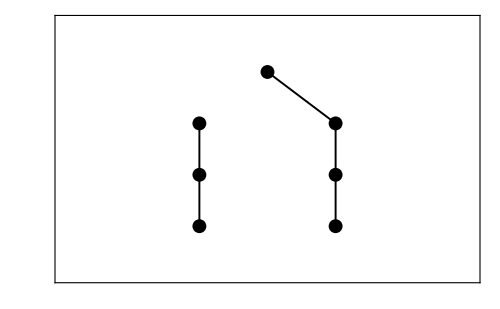

```mathematica
Build[DS[Chain[3],Chain[4]],ppp1]
Diagram[ppp1]
```

Next we take the cartesian product of the last poset (named Poset1) with a 3-element chain.

Building poset ppp2  ...

Done

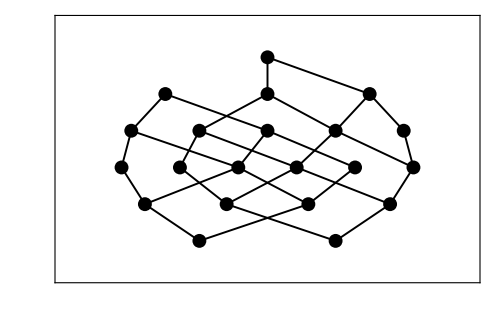

```mathematica
Build[CP[ppp1,Chain[3]],ppp2]
Diagram[ppp2]
```

Next we construct a more complicated example.  Here OS means "ordinal sum",  the operation of placing one poset above another.

```mathematica
strange=CP[OS[Chain[3],DS[Chain[2],Chain[4]]],Chain[3]];
Build[strange,ppp3]
```

Building poset ppp3  ...

Done

Notice that strange is not the "name" of the poset, but its "definition". The tag name in this case is ppp3.

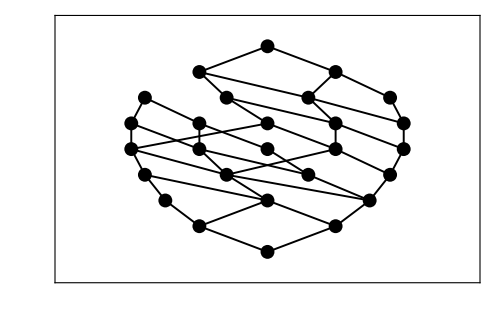

```mathematica
Diagram[ppp3]
```

### SELECTING A SUB-POSET

It is often convenient to define posets as subposets of another poset, with the induced partial order.  The BuildSubPoset command, with two options as input: either (1) a list of indices, or  (2) a Boolean function which picks out  indices in P[name] by doing a computation. We illustrate both methods by constructing the poset of subsets of 1...N whose sum is even, for  N=5 and N=6.

```mathematica
Build[Sets[5],sub5]
```

Building poset sub5  ...

Done

The following Boolean function returns True if the sum of elements in a set is even, and False otherwise.

```mathematica
evensumQ[s_]:=EvenQ[Apply[Plus,s]]
```

Using it, we produce a list of indices of the desired subposet.

```mathematica
evensets=Flatten[Position[Map[evensumQ,P[sub5]],True]]
```

{1,3,5,8,10,12,15,17,19,20,22,24,26,27,29,31}

The above result can also be obtained using the SpecialPoints command.

```mathematica
SpecialPoints[sub5,evensumQ]
```

{1,3,5,8,10,12,15,17,19,20,22,24,26,27,29,31}

#### First option for building a supbposet: list of indices.

The BuildSubposet command executes the Build command with this data, and performs a small amount of additional bookkeeping, for example it restores the original labels to the elements of the subposet.

```mathematica
BuildSubPoset[sub5,evensets,even5]
```

Building Subposet even5  ...

Building poset even5  ...

Done

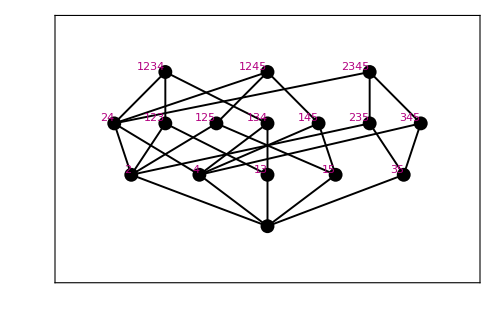

```mathematica
ChangeLabel[even5,Compact,1]
Diagram[even5,ShowLabels->1]
```

#### Second option for building a supbposet: Boolean function picks indices.

Here we supply evensumQ as an argument to BuildSubPoset.

```mathematica
Build[Sets[6],sub6]
BuildSubPoset[sub6,evensumQ,even6]
```

Building poset sub6  ...

Done

Building Subposet even6  ...

Building poset even6  ...

Done

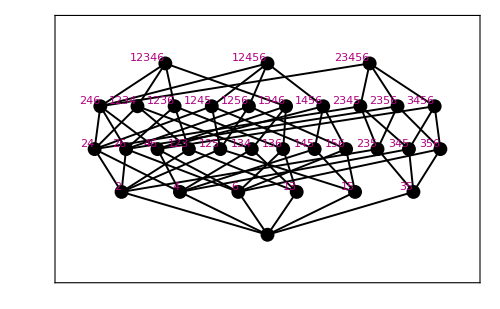

```mathematica
ChangeLabel[even6,Compact,1]
Diagram[even6,ShowLabels->1]
```

#### Another example : sets with no adjacent pairs

As another illustration,  we will construct the poset of subsets of {1,2,...,5} containing no two adjacent pairs. Every student of elementary combinatorics knows that the size of the resulting poset is a Fibonacci number.

```mathematica
nonadjQ[{___,x_,y_,___}]:=False/;y==x+1;
nonadjQ[{___}]:=True
```

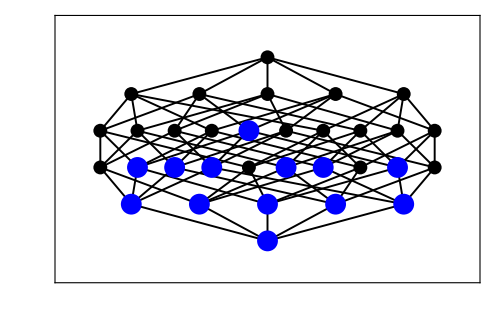

```mathematica
Diagram[sub5,SpecialPoints[sub5,nonadjQ]]
```

Building Subposet non5  ...

Building poset non5  ...

Done

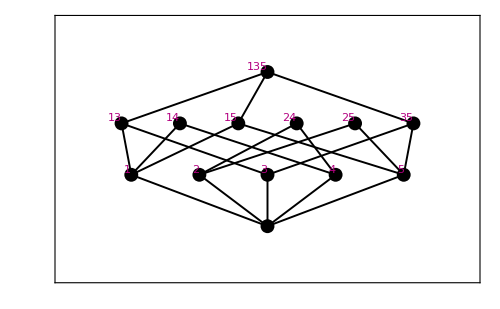

```mathematica
BuildSubPoset[sub5,nonadjQ,non5]
ChangeLabel[non5,Compact,1]
Diagram[non5,ShowLabels->1]
```

```mathematica
Card[non5]
```

13

Not surprisingly, it's a Fibonacci number. The dual poset is ranked (rank = size), but not strongly ranked.

Building poset non5dual  ...

Done

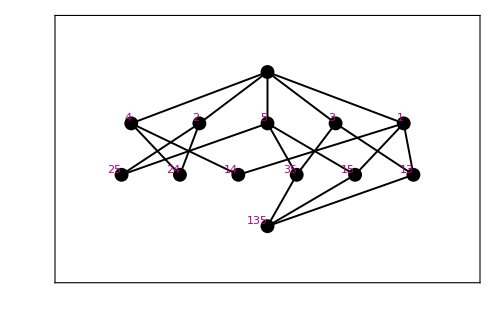

```mathematica
BuildDual[non5,non5dual]
ChangeLabel[non5dual,Compact,1]
Diagram[non5dual,ShowLabels->1]
```

```mathematica
{RankedQ[non5],StrongRankedQ[non5]}
{RankedQ[non5dual],StrongRankedQ[non5dual]}
```

{True,True}

{True,False}

Building poset sub6  ...

Done

Building Subposet non6  ...

Building poset non6  ...

Done

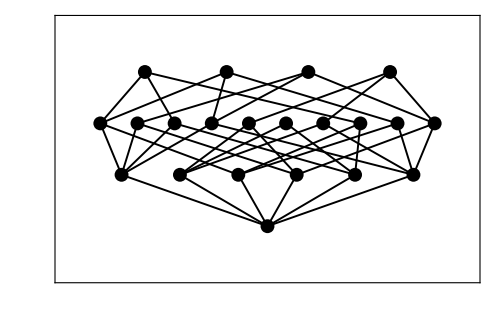

```mathematica
Build[Sets[6],sub6]
BuildSubPoset[sub6,nonadjQ,non6]
Diagram[non6]
```

```mathematica
Card[non6]
```

21

The cardinality of this poset (always a Fibonacci number) can be further refined by computing the rank generating function:

```mathematica
RGF[non6]
```

1+6 q+10 q^2+4 q^3

An easy combinatorial computation gets these coefficients directly, in terms of Binomial coeffients:

```mathematica
∑_(k=0)^6 Binomial[6-k+1,k] q^k
```

1+6 q+10 q^2+4 q^3

### INTERVAL SUB-POSETS

The interval sub-poset defined by elements A < B in P is the collection of all elements X in P such that A ≤ X ≤ B.  The command IntervalP[name,A,B] returns the indices corresponding to such an interval. Then BuildSubPoset[name,indices,newname] may be used to construct the poset.

We illustrate by constructing the interval in SetP[5] consisting of partitions that lie between partitions A = {1,2,3,4,5}  and B = {1,1,3,3,3}. Since A is the bottom element of the poset, the result may also be described as the principal order ideal generated by B.

```mathematica
Build[SetP[5],setp5]
```

Building poset setp5  ...

Done

```mathematica
indices=IntervalP[setp5,{1,2,3,4,5},{1,1,3,3,3}]
BuildSubPoset[setp5,indices,subp5]
```

{1,2,9,10,11,15,16,17,36,43}

Building Subposet subp5  ...

Building poset subp5  ...

Done

The elements of the interval are displayed in the following diagram as "special points".

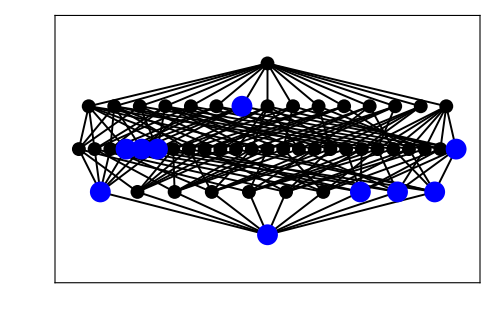

```mathematica
Diagram[setp5,indices]
```

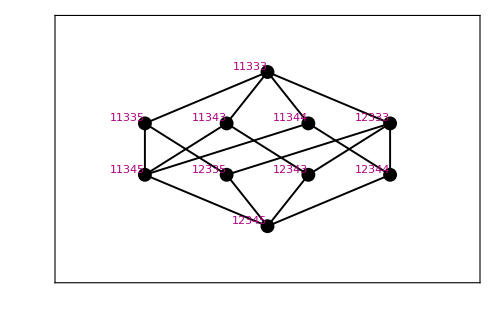

```mathematica
ChangeLabel[subp5,Compact,1]
Diagram[subp5,ShowLabels->1]
```

The IntervalQ command tests whether a set of indices defines an interval subposet.

```mathematica
IntervalQ[setp5,indices]
```

True

### LINEAR EXTENSIONS

A linear extension of a poset P with n elements is an order-preserving bijection from P to an n-element chain, i.e., an order-embedding of P in a total order.  Since both P and the chain are indexed by 1...n, we may represent such a map by a permutation of 1...n.  The command LinearExtensions[name] generates all such permutations.  Each one is represented by a list in which k appears in position i if P[[i]] is mapped to k by the linear extension. Linear extensions are also sometimes called natural labelings of P.

Closely related to linear extensions are the topological sortings of P, generated by the command TopSortings[name]. These are the inverses of the permutations in LinearExtensions[name], i.e. each one is represented by a list in which index i appears in position k if P[[i]] is mapped to the kth element of the chain. One can view topological sortings as linear arrangements of the indices that respect the order structure of P, i.e. index i precedes index j whenever P[[i]] < P[[j]] in P.

TopSortings[name] computes the Jordan - Hölder Set of P, denoted ℒ(P), as defined in Stanley' s Enumerative Combinatorics, Vol 1, Chapter 3.

A potential point of confusion is that, in this package, linear extensions are represented by means of indices, not elements or labels of elements. In most cases, this causes no confusion. However, the distinction is important when the elements or labels of P are also integers, and could be confused with indices. For example, these labels might correspond to an alternate indexing scheme.  It may be helpful to keep the following points in mind:

 --- the elements of P are objects appearing in the list P[name]
 --- Labels[name][[1]] and Labels[name][[2]] are two potentially different (and configurable) lists of labels of elements of P
 --- the entries in Labels[name][[2]] are initially set equal to the indices of elements of P, as created by the Build command. Indices always correspond to both a natural labeling and a topological sorting of P, i.e.,  x < y implies index(x) < index(y).

The following example illustrates these ideas, as well as some of the pitfalls. ZigZag posets are constructed by defining an "up-down" order pattern on the integers 1...n. Note that these integers are the elements of P -- not indices. They do not respect the ordering of P.

Building poset zz4  ...

Done

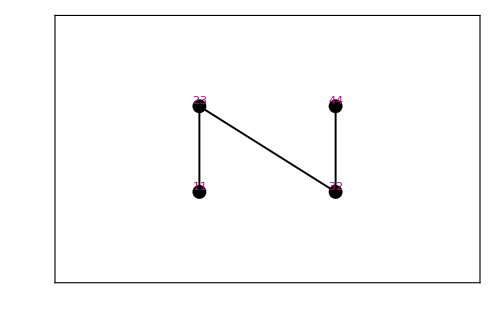

```mathematica
Build[ZigZag[4],zz4]
Diagram[zz4,ShowLabels->{1,2}]
```

In this diagram, elements of P[zz4] are represented by red labels, and their indices are represented by blue labels. The linear extension corresponding to blue labels is the function 1 → 1, 2 → 3, 3 → 2, 4 → 4, and the corresponding topological sorting is {1,3,2,4}. However, since in this package both objects are represented in terms of indices, both are represented by the identity permutation, which always appears in the output of LinearExtensions and TopSortings.

```mathematica
P[zz4]
Labels[zz4]
```

{1,3,2,4}

{{1,3,2,4},{1,2,3,4}}

```mathematica
LinearExtensions[zz4]
TopSortings[zz4]
```

{{3,1,4,2},{2,1,4,3},{2,1,3,4},{1,2,4,3},{1,2,3,4}}

{{2,4,1,3},{2,1,4,3},{2,1,3,4},{1,2,4,3},{1,2,3,4}}

Notice that, as permutations of 1…n, linear extensions and topological sortings are inverses of each other, and that the identity permutation {1,2,3,4} appears in both lists.

Now, another example of linear extensions, illustrating a more complicated case, :

```mathematica
Build[OS[OS[OS[Antichain[2],Chain[1]],ZigZag[5]],Chain[2]],posetx]
```

Building poset posetx  ...

Done

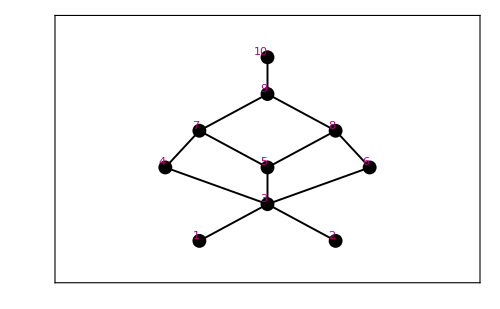

```mathematica
Diagram[posetx,ShowLabels->2]
```

```mathematica
TopSortings[posetx]
LinearExtensions[posetx]
```

{{2,1,3,6,5,8,4,7,9,10},{2,1,3,6,5,4,8,7,9,10},{2,1,3,6,5,4,7,8,9,10},{2,1,3,5,6,8,4,7,9,10},{2,1,3,5,6,4,8,7,9,10},{2,1,3,5,6,4,7,8,9,10},{2,1,3,5,4,7,6,8,9,10},{2,1,3,5,4,6,8,7,9,10},{2,1,3,5,4,6,7,8,9,10},{2,1,3,6,4,5,8,7,9,10},{2,1,3,6,4,5,7,8,9,10},{2,1,3,4,6,5,8,7,9,10},{2,1,3,4,6,5,7,8,9,10},{2,1,3,4,5,7,6,8,9,10},{2,1,3,4,5,6,8,7,9,10},{2,1,3,4,5,6,7,8,9,10},{1,2,3,6,5,8,4,7,9,10},{1,2,3,6,5,4,8,7,9,10},{1,2,3,6,5,4,7,8,9,10},{1,2,3,5,6,8,4,7,9,10},{1,2,3,5,6,4,8,7,9,10},{1,2,3,5,6,4,7,8,9,10},{1,2,3,5,4,7,6,8,9,10},{1,2,3,5,4,6,8,7,9,10},{1,2,3,5,4,6,7,8,9,10},{1,2,3,6,4,5,8,7,9,10},{1,2,3,6,4,5,7,8,9,10},{1,2,3,4,6,5,8,7,9,10},{1,2,3,4,6,5,7,8,9,10},{1,2,3,4,5,7,6,8,9,10},{1,2,3,4,5,6,8,7,9,10},{1,2,3,4,5,6,7,8,9,10}}

{{2,1,3,7,5,4,8,6,9,10},{2,1,3,6,5,4,8,7,9,10},{2,1,3,6,5,4,7,8,9,10},{2,1,3,7,4,5,8,6,9,10},{2,1,3,6,4,5,8,7,9,10},{2,1,3,6,4,5,7,8,9,10},{2,1,3,5,4,7,6,8,9,10},{2,1,3,5,4,6,8,7,9,10},{2,1,3,5,4,6,7,8,9,10},{2,1,3,5,6,4,8,7,9,10},{2,1,3,5,6,4,7,8,9,10},{2,1,3,4,6,5,8,7,9,10},{2,1,3,4,6,5,7,8,9,10},{2,1,3,4,5,7,6,8,9,10},{2,1,3,4,5,6,8,7,9,10},{2,1,3,4,5,6,7,8,9,10},{1,2,3,7,5,4,8,6,9,10},{1,2,3,6,5,4,8,7,9,10},{1,2,3,6,5,4,7,8,9,10},{1,2,3,7,4,5,8,6,9,10},{1,2,3,6,4,5,8,7,9,10},{1,2,3,6,4,5,7,8,9,10},{1,2,3,5,4,7,6,8,9,10},{1,2,3,5,4,6,8,7,9,10},{1,2,3,5,4,6,7,8,9,10},{1,2,3,5,6,4,8,7,9,10},{1,2,3,5,6,4,7,8,9,10},{1,2,3,4,6,5,8,7,9,10},{1,2,3,4,6,5,7,8,9,10},{1,2,3,4,5,7,6,8,9,10},{1,2,3,4,5,6,8,7,9,10},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
Length[TopSortings[posetx]]
```

32

So there are 32 linear extensions / topological sortings of this poset.  One can appreciate topological sortings (the first output) as "natural labeling" by tracking the elements in the listed order as they are added to the poset, thus generating a “growth diagram” of labeled elements.

### P-PARTITIONS; ORDER POLYNOMIALS

Several interesting combinatorial invariants of a poset may be constructed easily, once the linear extensions have been computed. For more mathematical details about these constructions, the reader is referred to Stanley's EC1 .

A P-partition is an order-preserving map from P to the nonnegative integers.  It is standard to introduce a generating function G[P,q] which enumerates P-partitions according to their part sums.  It can be shown that G[P,q] is a rational function whose numerator enumerates topological sortings by major index.  (The major index of a permutation is the sum of the indices of its decents.)

Building poset twochains  ...

Done

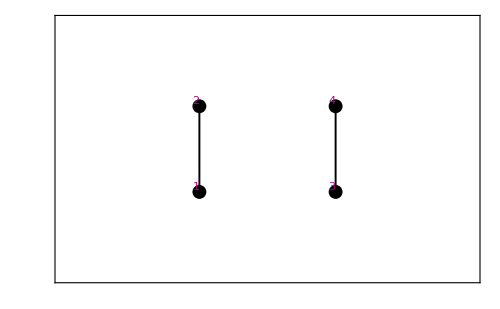

```mathematica
Build[DS[Chain[2],Chain[2]],twochains]
Diagram[twochains,ShowLabels->1]
```

```mathematica
G[twochains,q]
```

(1+q+2 q^2+q^3+q^4)/((1-q) (1-q^2) (1-q^3) (1-q^4))

```mathematica
Series[%,{q,0,20}]
```

1+2 q+5 q^2+8 q^3+14 q^4+20 q^5+30 q^6+40 q^7+55 q^8+70 q^9+91 q^10+112 q^11+140 q^12+168 q^13+204 q^14+240 q^15+285 q^16+330 q^17+385 q^18+440 q^19+506 q^20+O[q]^21

Observe that there are six topological sortings whose major index is distributed according to the numerator of the expression just computed:

```mathematica
TopSortings[twochains]
Map[MAJ,%]
```

{{2,4,1,3},{2,1,4,3},{2,1,3,4},{1,3,2,4},{1,2,4,3},{1,2,3,4}}

{2,4,1,2,3,0}

To check the coefficient of q^3 above, one can verify that there are eight P-partitions of 3 :

```mathematica
checkmap[x_] := (x[[1]]≤ x[[2]])&&(x[[3]]≤ x[[4]])
sum[x_] := Apply[Plus,x]
Select[Tuples[Range[0,3],4],(checkmap[#]&&(sum[#]==3))&]
```

{{0,0,0,3},{0,0,1,2},{0,1,0,2},{0,1,1,1},{0,2,0,1},{0,3,0,0},{1,1,0,1},{1,2,0,0}}

A related object is the "order polynomial" of a poset P, which counts order-preserving maps from P into an n-element chain.  It also has a rational generating function H_P(q), in which the numerator is equal to q times the enumerator for topological sortings by "descents".

```mathematica
OmegaGF[twochains,q]
```

(q+4 q^2+q^3)/(1-q)^5

```mathematica
Series[%,{q,0,20}]
```

q+9 q^2+36 q^3+100 q^4+225 q^5+441 q^6+784 q^7+1296 q^8+2025 q^9+3025 q^10+4356 q^11+6084 q^12+8281 q^13+11025 q^14+14400 q^15+18496 q^16+23409 q^17+29241 q^18+36100 q^19+44100 q^20+O[q]^21

Again we can see that the numerator gives the distribution of topological sortings by number of descents (plus 1):

```mathematica
Map[DES,TopSortings[twochains]]
```

{1,2,1,1,1,0}

For example, to check the coefficient of q^4 in H_P(q) above, one can verify that there are 100 order-preserving maps from P into a 3-element chain.

```mathematica
checkmap[x_] := (x[[1]]≤ x[[2]])&&(x[[3]]≤ x[[4]])
Select[Tuples[Range[0,3],4],checkmap]//Length
```

100

The order polynomial itself is the coefficient Ω_P(n) of q^n in

```mathematica
Factor[Omega[twochains,n]]
```

1/4 n^2 (1+n)^2

It is easy to verify directly that this answer is correct, i.e.

```mathematica
Sum[1/4 n^2 (1+n)^2 q^n,{n,0,Infinity}]
```

-(q (1+4 q+q^2))/(-1+q)^5

### MAXIMUM-SIZED ANTICHAINS; MINIMUM CHAIN COVERS.

The command MaxAntichain[P] returns the indices of a maximum-sized antichain in P, and simultaneously computes the links in a minimum-sized covering of P by chains. This information is stored in DilworthCover[P] (after the celebrated theorem of Dilworth, which states that the cardinalities of these two objects are the same).

Building poset sub3  ...

Done

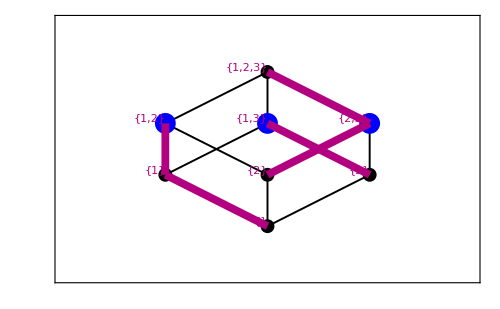

```mathematica
Build[Sets[3],sub3]
Diagram[sub3,MaxAntichain[sub3],DilworthCover[sub3],ShowLabels->1]
```

```mathematica
MaxAntichain[sub3]
```

{5,6,7}

```mathematica
DilworthCover[sub3]
```

{{1,2},{2,5},{3,7},{4,6},{7,8}}

And a more complicated example:

```mathematica
MaxAntichain[y52211]
```

{28,29,30,31,32,33,34,35,36}

We can highlight these objects in the diagram:

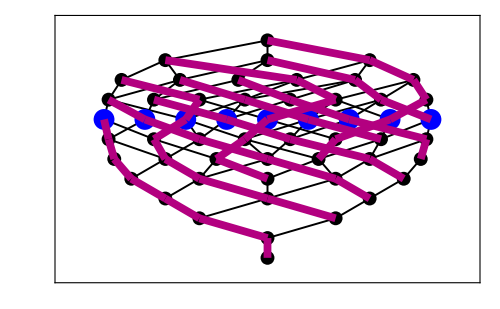

```mathematica
Diagram[y52211,MaxAntichain[y52211],DilworthCover[y52211]]
```

## 5. Defining a Poset by its Covering Function

In this section we give several examples illustrating the process by which a "new" poset can be constructed from a  formal description (in Mathematica) of its covering function.

#### CHIP-FIRING POSETS

Consider this example: a pile of N stones is placed at the origin of a 1-dimensional grid, indexed by the integers.   Subsequent moves consist of taking two stones located at position k, and distributing them one each to positions k-1 and k+1.   The possible configurations of stones frm a poset, in which coverings correspond to allowable moves. This poset has been studied by A. Bjorner, L. Lovasz, and P. Shor in a paper called "Chip-firing games on graphs" .

States of the game are represented by strings of length N+1, with the initial state represented by a string with N in position Floor[N/2+1], and zeros elsewhere. For example, if N=5, the initial state is {0,0,5,0,0,0}.

The first step is to write a Mathematica program to generate, from a given state, a list of those states obtainable from it by an allowable move.

```mathematica
fire[state_]:=Block[{coverlist={},i,new},Do[If[state⟦i⟧>1,new=state;new⟦i-1⟧++;new⟦i+1⟧++;new⟦i⟧--;new⟦i⟧--;AppendTo[coverlist,new]],{i,2,Length[state]-1}];Return[coverlist]]
```

Next we define the initial state.

```mathematica
initialstate[N_]:=Table[If[i==Floor[N/2+1],N,0],{i,N+1}]
```

Finally, the poset "definition" is a triple consisting of (1) the name of the covering function, (2) a list of all starting states (in this case only one), and (3) a number which is sure to be larger than the length of the longest chain generated. In this case we choose N^3, though in general it's not always clear in advance what this bound should be.

```mathematica
chipfire[N_]:={fire,{initialstate[N]},N^3};
```

Now the poset can be "built".

```mathematica
Build[chipfire[5],chip5]
```

Building poset chip5  ...

Done

```mathematica
P[chip5]
```

{{0,0,5,0,0,0},{0,1,3,1,0,0},{0,2,1,2,0,0},{1,0,2,2,0,0},{0,2,2,0,1,0},{1,1,0,3,0,0},{1,0,3,0,1,0},{0,3,0,1,1,0},{1,1,1,1,1,0}}

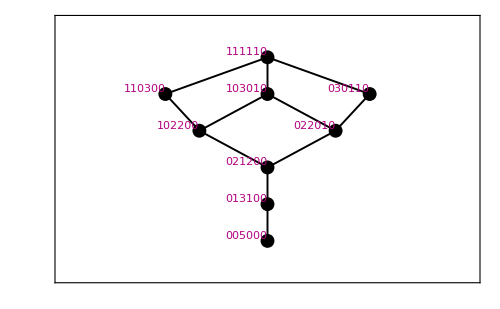

```mathematica
ChangeLabel[chip5,Compact,1]
Diagram[chip5,ShowLabels->1]
```

Building poset chip7  ...

Done

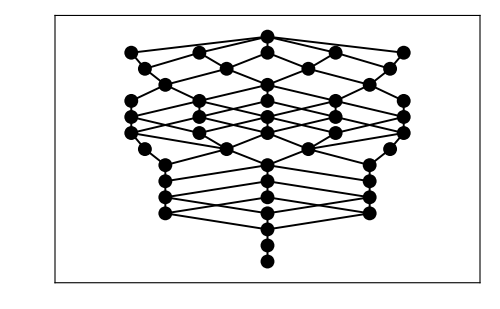

True

```mathematica
Build[chipfire[7],chip7]
Diagram[chip7]
LatticeQ[chip7]
```

```mathematica
Build[chipfire[8],chip8]
Diagram[chip8,Manipulate->True];
```

Building poset chip8  ...

Done

## Appendix: List of All Commands

For more information about a particular command, type

```mathematica
Information["<command>",LongForm->False]
```

For example:

```mathematica
Information["DownDegree",LongForm->False]
```

DownDegree[name][[x]] is the number of 
elements covered by P[name][[x]].

To see a list of all Poset commands containing a particular string, type

```mathematica
ListCommands["string"]
```

or

```mathematica
Information["Posets`*string*",LongForm->True]
```

For example:

```mathematica
ListCommands["Build"]
```

(Build | BuildSubPoset
BuildDual | ---)

For a complete list of all commands known to Posets, type

```mathematica
ListCommands[]
```

(AllTableaux | MeetSubLattice
AMAJ | MeetSubLatticeQ
Antichain | MI
ASC | MICoverRelations
Background1 | MinElements
Background2 | MSL
Build | Mu
BuildDual | NewLabel
BuildSubPoset | NK
Card | NonXP
Chain | NumLattices
ChainsBetweenGF | NumP
ChangeLabel | NumPosets
CharPoly | Omega
CleanRank | OmegaBar
CoCovers | OmegaBarGF
Compact | OmegaGF
ContractionLattice | OrderIdeal
CoverRelations | OrderIdealQ
Covers | OrderIdeals
CP | OrdinalSum
CProduct | OS
DES | P
Diagram | PGraded
DilworthCover | PGradedIndices
DisjointSum | PolyToGF
DistributiveLatticeQ | PosetP
Div | RandomP
DownDegree | Rank
Downs | RankedQ
DS | ResetLabel
DualOrderIdeal | RGF
DualOrderIdealQ | RWeakS
DualOrderIdeals | SavedSettings
Ferrers | SaveOne
Fuse | SetP
G | Sets
GBar | ShowLabels
GenFun | Silent
GetIsomorphism | SL
GFToPoly | SortByRanks
H | SP
InfiniteProduct | SpecialPoints
IntervalP | SPM
IntervalQ | STableaux
InversionCode | StrictDowns
IsomorphicQ | StrictUps
JI | StrongRankedQ
JICoverRelations | StrongS
JofP | SubLattice
JoinL | SubLatticeQ
JoinSubLattice | Subwords
JoinSubLatticeQ | Tabify
JSL | TClosure
L | TensorProduct
Labels | ToMatrix
LatticeQ | ToPermutation
LinearExtensions | TopSort
ListCommands | TopSortings
LJoin | ToRelation
LMeet | UpDegree
LocateElement | Ups
LocateSet | Ver
LongestChain | WeakS
L$ | YoungsLattice
MAJ | Zap
MajP | ZeroDiffs
MaxAntichain | ZetaJI
MaxElements | ZetaMI
MaximalChainsDown | ZetaP
MaximalChainsUp | ZetaPoly
MeetL | ZigZag)

For more information about each command, please consult the "usage" section of the package. This  gives the precise syntax for each command, and can even be printed out as a compact "user's manual", if desired.